№12.445 Используя теоремы о вычетах, вычислить следующий интеграл:

f(z)=∫_(|z|=5) z^2/(cos(z)(sin(z))^3)ⅆz

Данная задача примечательна тем, что имеет бесконечное число полюсов, поэтому нам придется выбрать лишь те, что входят в контур |z|=5.

Зададим функцию:

```mathematica
f[z_]:=z^2/(Sin[z]^3 Cos[z])
```

И найдем полюса:

```mathematica
Solve[Sin[z]^3 Cos[z]==0,z]
```

{{z→ConditionalExpression[2 π C[1],C[1]∈Integers]},{z→ConditionalExpression[-π/2+2 π C[1],C[1]∈Integers]},{z→ConditionalExpression[π/2+2 π C[1],C[1]∈Integers]},{z→ConditionalExpression[π+2 π C[1],C[1]∈Integers]}}

Представим в более удобной для нас форме:

```mathematica
sol[n_]:={{z->π n},{z->π/2+π n}}
```

Найдем все кори при n=-2,...1 (функция Flatten нужна для того чтобы создать плоское, единое множество корней):

```mathematica
Flatten[Table[z/.sol[i] ,{i,-2,1}],1]
```

{-2 π,-(3 π)/2,-π,-π/2,0,π/2,π,(3 π)/2}

Как мы видим все, кроме первого лежат внутри конутра. Покажем это графически:

```mathematica
Show[ContourPlot[x^2+y^2==25,{x,-7,7},{y,-7,7},Frame->False,Axes->True],Graphics[{PointSize[Large],Red,Point[Flatten[ReIm[z/.sol[#]&/@{1,0,-1,-2} ],1]]}]]
```

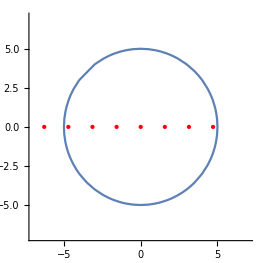

Создадим список полюсов, лежащих внутри конутра:

```mathematica
sol1=Flatten[Table[z/.sol[i] ,{i,-2,1}],1][[2;;]]
```

{-(3 π)/2,-π,-π/2,0,π/2,π,(3 π)/2}

Применим функцию Residue для каждого корня:

```mathematica
Residue[f[z],{z,sol1[[#]]}]&/@Range[7]
```

{-(9 π^2)/4,1+π^2,-π^2/4,1,-π^2/4,1+π^2,-(9 π^2)/4}

По первой теореме о вычетах, искомый интеграл будет равен:

```mathematica
int=2 π ⅈ Sum[Residue[f[z],{z,sol1[[i]]}],{i,1,Length[sol1]}]
```

2 ⅈ π (3-3 π^2)

Получили ответ

∫_(|z|=5) z^2/(cos(z)(sin(z))^3)ⅆz=2 ⅈ π (3-3 π^2)